```mathematica
Exit
```

```mathematica
Needs["PM`"];
LoadPackages["Geometries"]

TestEigensystem[λ_,U_,A_]:=Max[Abs[Transpose[U].Conjugate[λ U]-A]];
TestEigensystem2[λ_,U_,A_]:=Max[Abs[ConjugateTranspose[U].A.U-DiagonalMatrix[λ]]];
```

WARNING: LTemplate has not yet been tested with Mathematica 13.2.1.
The latest supported Mathematica version is 12.3.1.
Please report any issues you find to szhorvat at gmail.com.

```mathematica
type=Complex;
matrixCount=100000;
n=3;
If[type===Real,
A=ToPack[#ᵀ.#&/@RandomReal[{-1,1},{matrixCount,n,n}]];
,
A=ToPack[ConjugateTranspose[#].#&/@RandomComplex[{-1-I,1+I},{matrixCount,n,n}]];
];
```

```mathematica
{λTrue,UTrue}=Transpose[Eigensystem/@A];//AbsoluteTiming
Max[MapThread[TestEigensystem,{λTrue,UTrue,A}]]
Max[MapThread[TestEigensystem2,{λTrue,Transpose/@UTrue,A}]]
```

{0.450948,Null}

1.42109×10^-14

2.13169×10^-14

```mathematica
{λ,U}=HermitianEigensystems[A,Method->"LowDimensional"];//RepeatedTiming
errors=MapThread[TestEigensystem2,{λ,U,A}];
Max[errors]
Mean[errors]
Median[errors]
```

{0.00486148,Null}

1.83295×10^-10

6.46351×10^-15

1.4433×10^-15

```mathematica
{λ,U}=HermitianEigensystems[A,Method->"LowDimensional","SinglePrecision"->True];//RepeatedTiming
errors=MapThread[TestEigensystem2,{λ,U,A}];
Max[errors]
Mean[errors]
Median[errors]
```

{0.00407983,Null}

0.000922205

1.03293×10^-6

6.80325×10^-7

```mathematica
{λ,U}=HermitianEigensystems[A,Method->"LAPACK"];//RepeatedTiming
errors=MapThread[TestEigensystem2,{λ,U,A}];
Max[errors]
Mean[errors]
Median[errors]
```

{0.0188253,Null}

1.06582×10^-14

1.47764×10^-15

1.33227×10^-15

```mathematica
{λ,U}=HermitianEigensystems[A,Method->"LAPACK","SinglePrecision"->True];//RepeatedTiming
errors=MapThread[TestEigensystem2,{λ,U,A}];
Max[errors]
Mean[errors]
Median[errors]
```

{0.0179936,Null}

4.35117×10^-6

6.67909×10^-7

5.68389×10^-7

```mathematica
(*{λ2,U2}=Eigensystems3D[A];//AbsoluteTiming
(*{λ2,U2}=Eigensystems2D[A];//AbsoluteTiming*)
errors=MapThread[TestEigensystem,{λ2,U2,A}];
Max[errors]
Mean[errors]
Median[errors]*)
```

```mathematica
{Q,H}=HessenbergDecomposition[A[[3]]];
Max[Abs[Im[H]]]
H=Re[H]
H[[1,3]]=0.;
```

4.44089×10^-16

{{1.53569,2.0103,2.15814×10^-17},{2.0103,3.71765,1.35879},{0.,1.35879,2.01572}}

```mathematica
Chop[H]//MatrixForm
```

(1.90147 | -2.32295 | 0
-2.32295 | 3.84136 | 0.343821
0 | 0.343821 | 0.683377)

```mathematica
H//MatrixForm
```

(1.90147 | -2.32295 | 0.
-2.32295 | 3.84136 | 0.343821
0. | 0.343821 | 0.683377)

```mathematica
H=DiagonalMatrix[{a,b,c}]+DiagonalMatrix[{d,e},1]+DiagonalMatrix[{d,e},-1]
```

{{a,d,0},{d,b,e},{0,e,c}}

```mathematica
λ=.
```

```mathematica
CoefficientRules[Det[H-λ IdentityMatrix[3]],λ]
```

{{3}→-1,{2}→a+b+c,{1}→-a b-a c-b c+d^2+e^2,{0}→a b c-c d^2-a e^2}

```mathematica
Det[H]==λ[1]λ[2]λ[3]
Tr[H]==λ[1]+λ[2]+λ[3]
Expand[(Tr[H.H]-Expand[Tr[H]^2])/2]==λ[1]λ[2]+λ[2]λ[3]+λ[3]λ[1]
```

5.71447

6.42621

5.71447

1.07922

```mathematica
Det[H]
```

a b c-c d^2-a e^2

```mathematica
Tr[Inverse[H]]//Simplify
```

(b c+a (b+c)-d^2-e^2)/(a b c-c d^2-a e^2)

```mathematica
Solve[
{T[1]==λ[1]+λ[2]+λ[3],
T[2]==1/λ[1]+1/λ[2]+1/λ[3],
T[3]==λ[1]λ[2]λ[3]
},{λ[1],λ[2],λ[3]}
]
```

```mathematica
T[1]=Tr[H]
T[2]=(Expand[Tr[H]^2]-Tr[H.H])/2
T[3]=Det[H]

ClearAll[λ];
ClearAll[T];
sol=Solve[
{T[1]==λ[1]+λ[2]+λ[3],
T[2]==λ[1]λ[2]+λ[2]λ[3]+λ[3]λ[1],
T[3]==λ[1]λ[2]λ[3]
},{λ[1],λ[2],λ[3]}
];

λ1=(λ[1]/.sol[[1]])//FullSimplify
```

7.26905

10.4108

0.526575

```mathematica
T[1]=Tr[H]
T[2]=(Expand[Tr[H]^2]-Tr[H.H])/2
T[3]=Det[H]
```

7.26905

10.4108

0.526575

```mathematica
λ1
```

0.0524895+1.11022×10^-16 ⅈ

```mathematica
√(-T[1]^2 T[2]^2+4 T[2]^3+4 T[1]^3 T[3]-18 T[1] T[2] T[3]+27 T[3]^2)
```

0.+33.3806 ⅈ

```mathematica
√(-T[1]^2 T[2]^2+4 T[2]^3+4 T[1]^3 T[3]-18 T[1] T[2] T[3]+27 T[3]^2)
```

0.+33.3806 ⅈ

```mathematica
FullSimplify[Cos[ArcCos[r]/3+2/3Pi],r∈Reals]
```

-Sin[1/6 (π+2 ArcCos[r])]

```mathematica
Cos[ArcCos[r]/3+2/3Pi]
```

```mathematica
Cos[ArcCos[r]/3]Cos[2/3Pi]-Sin[ArcCos[r]/3]Sin[2/3Pi]
```

-1/2 Cos[ArcCos[r]/3]-1/2 √3 Sin[ArcCos[r]/3]

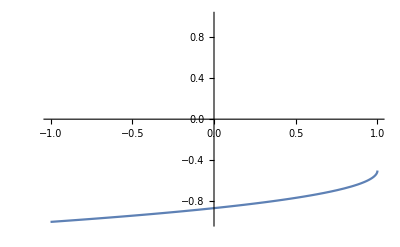

```mathematica
Plot[Cos[ArcCos[r]/3+2/3Pi],{r,-1,1},PlotRange->{-1,1}]
```

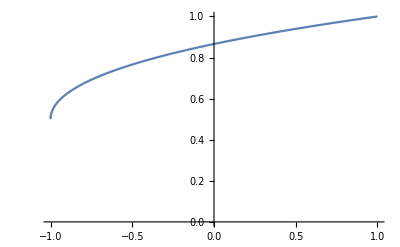

```mathematica
Plot[Cos[ArcCos[r]/3],{r,-1,1},PlotRange->{0,1}]
```

```mathematica
λ1//Together
```

(-2 2^(1/3) T[1]^2+6 2^(1/3) T[2]+2 T[1] (-2 T[1]^3+9 T[1] T[2]-27 T[3]+3 √3 √(-T[1]^2 T[2]^2+4 T[2]^3+4 T[1]^3 T[3]-18 T[1] T[2] T[3]+27 T[3]^2))^(1/3)-2^(2/3) (-2 T[1]^3+9 T[1] T[2]-27 T[3]+3 √3 √(-T[1]^2 T[2]^2+4 T[2]^3+4 T[1]^3 T[3]-18 T[1] T[2] T[3]+27 T[3]^2))^(2/3))/(6 (-2 T[1]^3+9 T[1] T[2]-27 T[3]+3 √3 √(-T[1]^2 T[2]^2+4 T[2]^3+4 T[1]^3 T[3]-18 T[1] T[2] T[3]+27 T[3]^2))^(1/3))

```mathematica
{λ[1],λ[2],λ[3]}=Eigenvalues[H]
```

{5.33678,1.87979,0.0524895}

```mathematica
λ[1]λ[2]λ[3]
```

1.07922

```mathematica
λ[1]λ[2]+λ[2]λ[3]+λ[3]λ[1]
```

5.71447

```mathematica
T[2]
```

-5.71447

-a b-a c-b c+d^2+e^2==λ[1] λ[2]+λ[1] λ[3]+λ[2] λ[3]

-a b-a c-b c+d^2+e^2

```mathematica
Tr[H.H.H]
```

2 d (a d+b d)+a (a^2+d^2)+2 e (b e+c e)+c (c^2+e^2)+b (b^2+d^2+e^2)

a^2+b^2+c^2+2 d^2+2 e^2

a+b+c

```mathematica
F@@Join[Diagonal[H],Diagonal[H,1]]
Δ@@Join[Diagonal[H],Diagonal[H,1]]
```

5.40609-3.70074×10^-17 ⅈ

-3737.42

```mathematica
Δ[a_,b_,c_,d_,e_]=((a+b-2 c) ((2 a-b-c) (a-2 b+c)+9 d^2)+9 (-2 a+b+c) e^2)^2-4 (a^2+b^2-b c+c^2-a (b+c)+3 (d^2+e^2))^3;
```

```mathematica
F[a_,b_,c_,d_,e_]=FullSimplify[
ToRadicals[Eigenvalues[DiagonalMatrix[{a,b,c}]+DiagonalMatrix[{d,e},1]+DiagonalMatrix[{d,e},-1]][[1]]]
]
```

1/6 (2 (a+b+c)+(2 2^(1/3) (a^2+b^2-b c+c^2-a (b+c)+3 (d^2+e^2)))/(2 a^3+2 b^3-3 b^2 c-3 b c^2+2 c^3-3 a^2 (b+c)+9 b d^2-18 c d^2+9 b e^2+9 c e^2-3 a (b^2-4 b c+c^2-3 d^2+6 e^2)+√(((a+b-2 c) ((2 a-b-c) (a-2 b+c)+9 d^2)+9 (-2 a+b+c) e^2)^2-4 (a^2+b^2-b c+c^2-a (b+c)+3 (d^2+e^2))^3))^(1/3)+2^(2/3) (2 a^3+2 b^3-3 b^2 c-3 b c^2+2 c^3-3 a^2 (b+c)+9 b d^2-18 c d^2+9 b e^2+9 c e^2-3 a (b^2-4 b c+c^2-3 d^2+6 e^2)+√(((a+b-2 c) ((2 a-b-c) (a-2 b+c)+9 d^2)+9 (-2 a+b+c) e^2)^2-4 (a^2+b^2-b c+c^2-a (b+c)+3 (d^2+e^2))^3))^(1/3))

```mathematica
√(4 (-a^2+a b-b^2+a c+b c-c^2-3 d^2-3 e^2)^3+(2 a^3-3 a^2 b-3 a b^2+2 b^3-3 a^2 c+12 a b c-3 b^2 c-3 a c^2-3 b c^2+2 c^3+9 a d^2+9 b d^2-18 c d^2-18 a e^2+9 b e^2+9 c e^2)^2)
```

```mathematica
√(4 (-a^2+a b-b^2+a c+b c-c^2-3 d^2-3 e^2)^3+(2 a^3-3 a^2 b-3 a b^2+2 b^3-3 a^2 c+12 a b c-3 b^2 c-3 a c^2-3 b c^2+2 c^3+9 a d^2+9 b d^2-18 c d^2-18 a e^2+9 b e^2+9 c e^2)^2)//FullSimplify
```

√(((a+b-2 c) ((2 a-b-c) (a-2 b+c)+9 d^2)+9 (-2 a+b+c) e^2)^2-4 (a^2+b^2-b c+c^2-a (b+c)+3 (d^2+e^2))^3)

```mathematica
HermitianEigensystem[H-IdentityMatrix[3] 0.30723673360050996,Method->"LowDimensional"]
```

Compiling cHermitianEigensystemD_3_Real64...

Compilation done. Time elapsed = 0.933458 s.

{{-0.0432059,5.09886,0.448848},{{0.739039,0.551466,0.386919},{0.520948,-0.831995,0.19078},{-0.427124,-0.0605705,0.902162}}}

```mathematica
cSmallestEigenvalueD[3,Real,False]
```

Compiling cSmallestEigenvalueD_3_Real64...

/Users/Henrik/Library/Mathematica/SystemFiles/LibraryResources/MacOSX-ARM64/Working-MacBook-Pro-6-97843-3861598976-9/cSmallestEigenvalueD_3_Real64.c:35:14: warning: unused variable 'tol' [-Wunused-variable]
        const SReal tol         = static_cast<SReal>(get<Real>(Args[2]));
                    ^
/Users/Henrik/Library/Mathematica/SystemFiles/LibraryResources/MacOSX-ARM64/Working-MacBook-Pro-6-97843-3861598976-9/cSmallestEigenvalueD_3_Real64.c:36:13: warning: unused variable 'max_iter' [-Wunused-variable]
        const Int  max_iter     = get<Int >(Args[3]);
                   ^
2 warnings generated.

Compilation done. Time elapsed = 0.789315 s.

LibraryFunction[…]

```mathematica
ClearAll[cSmallestEigenvalueD];
cSmallestEigenvalueD[d_Integer,type:Real|Complex,singleprecQ:True|False]:=cSmallestEigenvalueD[d,type,singleprecQ]= Module[{lib, libname, name, code, t},

	libname = name = "cSmallestEigenvalueD_"<>IntegerString[d]<>"_"<>ToString[type]<>If[singleprecQ,"32","64"];
	
	If[True,

		Print["Compiling "<>name<>"..."];

		code = StringJoin[
"
#define NDEBUG

#define TOOLS_ENABLE_PROFILER

#include \"WolframLibrary.h\"
#include \"MMA.hpp\"

#include \"Tensors.hpp\"

using namespace Tools;
using namespace Tensors;

using namespace mma;

using Real = mreal;
using Scal = "<>If[type===Real,"Real","std::complex<Real>"]<>";
using Int  = mint;

using SReal = "<>If[singleprecQ,"Real32","Real64"]<>";
using SScal = "<>If[type===Real,"SReal","std::complex<SReal>"]<>";

static constexpr Int n = "<>IntegerString[d]<>";

EXTERN_C DLLEXPORT int "<>name<>"(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res )
{
	//Profiler::Clear(\""<>$HomeDirectory<>"\");

	MTensor A_      = get<MTensor>(Args[0]);
	MTensor lambda_ = get<MTensor>(Args[1]);

	cptr<Scal> A            = data<Scal>(A_);
	mptr<Real> lambda       = data<Real>(lambda_);

	const SReal tol         = static_cast<SReal>(get<Real>(Args[2]));
	const Int  max_iter     = get<Int >(Args[3]);
	const Int  thread_count = std::max( Scalar::One<Int>, get<Int >(Args[4]) );

	const Int matrix_count  = dimensions( get<MTensor>(Args[0]) )[0];
	ParallelDo(
		[=]( const Int thread )
		{
			Tiny::SelfAdjointMatrix<n,SScal,Int> M;
			zerofy_buffer<n*n>( &M[0][0] );

			const Int k_begin = JobPointer( matrix_count, thread_count, thread     );
			const Int k_end   = JobPointer( matrix_count, thread_count, thread + 1 );

			const Int nn = n * n;

			for( Int k = k_begin; k < k_end; ++k )
			{
				M.Read( &A[nn * k] );
	
				lambda[k] = M.SmallestEigenvalue( tol, max_iter );
			}
		},
		thread_count
	);

	disown(lambda_);

	return LIBRARY_NO_ERROR;
}"];
		t = AbsoluteTiming[
			lib = CreateLibrary[
				code,
				libname,
				"Language"->"C++"
				,"CompileOptions"->{
		"-Wall","-Wextra","-Wno-unused-parameter"
		,"-mmacosx-version-min="<>StringSplit[Import["!sw_vers &2>1","Text"]][[4]]
		,"-std=c++20"
		,"-mcpu=native -mtune=native"
		,"-Ofast"
		,"-flto"
		,"-gline-tables-only"
		,"-gcolumn-info"
		(*,"-framework Accelerate"*)
		,"-pthread"
	}
	(*,"LinkerOptions"->{"-lm","-ldl","-lopenblas"}*)
         (*,"LinkerOptions"->{"-lm","-ldl","-lblas","-llapack"}*)
	(*,"LinkerOptions"->{"-lm","-ldl"}*)
	,"IncludeDirectories"->{$TensorsIncludeDirectory}
	,"LibraryDirectories"->{}
	,"ShellOutputFunction"->Print
]
		][[1]];
		Print["Compilation done. Time elapsed = ", t, " s.\n"];
	];

	LibraryFunctionLoad[lib,name,
		{{type,3,"Constant"},{Real,1,"Shared"},Real,Integer,Integer},
		"Void"
	]
];
```